Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos.

## Problemas. Tema 8. Funciones de varias variables

## 1.- Calcular, si existe, los límites de las siguientes funciones: a) Lim_((x,y)->(2,1))(4-xy)/(x^2+3 y^2) b) Lim_((x,y)->(0,0))(x^2-2xy+y^2)/(x-y) c) Lim_((x,y)->(2,2))(x-y)/(x^4-y^4) d) Lim_((x,y)->(2,-4))(y+4)/(x^2 y-xy+4 x^2-4x) e) Lim_((x,y)->(0,0))(x^2-xy)/(√x-√y) f) Lim_((x,y)->(0,0))(x^4-4 y^2)/(x^2+2y)

Solución:
	a) Lim_((x,y)->(2,1))(4-xy)/(x^2+3 y^2)=(4-2*1)/(2^2+3*1^2)=2/7
	
	b) Lim_((x,y)->(0,0))(x^2-2xy+y^2)/(x-y)=[0/0]=Lim_((x,y)->(0,0))(x-y)^2/(x-y)=Lim_((x,y)->(0,0))x-y=0
	
	c) Lim_((x,y)->(2,2))(x-y)/(x^4-y^4)=[0/0]=Lim_((x,y)->(2,2))(x-y)/((x^2-y^2)(x^2+y^2))==Lim_((x,y)->(2,2))(x-y)/((x-y)(x+y)(x^2+y^2))==Lim_((x,y)->(2,2))1/((x+y)(x^2+y^2))=1/32 
	
 	d) Lim_((x,y)->(2,-4))(y+4)/(x^2 y-xy+4 x^2-4x)=[0/0]=Lim_((x,y)->(2,-4))(y+4)/(xy(x-1)+4x(x-1))=Lim_((x,y)->(2,-4))(y+4)/((x-1)(xy+4x))=Lim_((x,y)->(2,-4))(y+4)/((x-1)x(y+4))=Lim_((x,y)->(2,-4))1/((x-1)x)=1/2 
 	
 	e) Lim_((x,y)->(0,0))(x^2-xy)/(√x-√y)=[0/0]=Lim_((x,y)->(0,0))(x(x-y))/(√x-√y)=Lim_((x,y)->(0,0))(x(√x-√y)(√x+√y))/(√x-√y)=Lim_((x,y)->(0,0))x(√x+√y)=0
 	
 	f) Lim_((x,y)->(0,0))(x^4-4 y^2)/(x^2+2y)=[0/0]=Lim_((x,y)->(0,0))((x^2+2y)(x^2-2y))/(x^2+2 y^2)=Lim_((x,y)->(0,0))x^2-2y=0

Con Mathematica

```mathematica
Limit[(4-x*y)/(x^2+3y^2),{x,y}->{2,1}]
```

2/7

```mathematica
Limit[(x^2-2x*y+y^2)/(x-y),{x,y}->{0,0}]
```

0

```mathematica
Limit[(x-y)/(x^4-y^4),{x,y}->{2,2}]
```

1/32

```mathematica
Limit[(y+4)/(x^2*y-x*y+4x^2-4x),{x,y}->{2,-4}]
```

1/2

```mathematica
Limit[(x^2-x*y)/(Sqrt[x]-Sqrt[y]),{x,y}->{0,0}]
```

0

```mathematica
Limit[(x^4-4y^2)/(x^2+2y),{x,y}->{0,0}]
```

0

## 2.- Calcular, si existe, el límite de función Lim_((x,y)->(0,0))(x^2 sen^2 y)/(x^2+2 y^2)

Solución:
Para calcular el límite haremos el cambio a coordenadas polares(x=ρ cosθ, y=ρ senθ).

Lim_((x,y)->(0,0))(x^2 sen^2 y)/(x^2+2 y^2)=Lim_(ρ->0)(ρ^2 cos^2 θ*sen^2(ρsenθ))/(ρ^2 cos^2 θ+2 ρ^2 sen^2 θ)=Lim_(ρ->0)(ρ^2 cos^2 θ*sen^2(ρsenθ))/(ρ^2(cos^2 θ+2 sen^2 θ))=Lim_(ρ->0)(cos^2 θ*sen^2(ρsenθ))/(cos^2 θ+2 sen^2 θ)=0

Cuando ρ → 0, la expresión tiende a 0, con independencia de los valores de θ.

El límite de la función en el punto (0,0) es cero.

Con Mathematica

```mathematica
Limit[(x^2*(Sin[y])^2)/(x^2+2y^2),{x,y}->{0,0}]
```

0

## 3.- Estudiar, utilizando el cambio a coordenadas polares, el límite de las funciones a) f(x,y)= (sen(x^2+y^2))/(x^2+y^2) en el punto (0,0) b) f(x,y)= xy/(√(x^2+y^2)) en el punto (0,0) c) f(x,y)= (x^3 y^2)/((x^2+y^2)^2) en el punto (0,0) d) f(x,y)= (3 x^2 y)/(2 x^2+2 y^2) en el punto (0,0)

Solución:
	a) Lim_((x,y)->(0,0))(sen(x^2+y^2))/(x^2+y^2)=Lim_(ρ->0)(sen(ρ^2 cos^2 θ+ρ^2 sen^2 θ))/(ρ^2 cos^2 θ+ρ^2 sen^2 θ)=Lim_(ρ->0)(sen(ρ^2(cos^2 θ+sen^2 θ)))/(ρ^2(cos^2 θ+sen^2 θ))=Lim_(ρ->0)(sen(ρ^2))/ρ^2=[ρ^2=t]=Lim_(ρ->0)(sen(t))/t=1
	
	b) Lim_((x,y)->(0,0))xy/(√(x^2+y^2))=Lim_(ρ->0)(ρcosθ*ρsenθ)/(√(ρ^2 cos^2 θ+ρ^2 sen^2 θ))=Lim_(ρ->0)(ρ^2 cosθ*senθ)/(√(ρ^2(cos^2 θ+sen^2 θ)))=Lim_(ρ->0)(ρ^2 cosθ*senθ)/(√(ρ^2))=Lim_(ρ->0)(ρ^2 cosθ*senθ)/ρ=Lim_(ρ->0)ρcosθ*senθ=0
	
	c) Lim_((x,y)->(0,0))(x^3 y^2)/((x^2+y^2)^2)=Lim_(ρ->0)(ρ^3 cos^3 θ*ρ^2 sen^2 θ)/((ρ^2 cos^2 θ+ρ^2 sen^2 θ)^2)=Lim_(ρ->0)(ρ^5 cos^3 θ*sen^2 θ)/((ρ^2(cos^2 θ+sen^2 θ))^2)=Lim_(ρ->0)(ρ^5 cos^3 θ*sen^2 θ)/((ρ^2)^2)=Lim_(ρ->0)ρcos^3 θ*sen^2 θ=0
	
	d) Lim_((x,y)->(0,0))(3 x^2 y)/(2 x^2+2 y^2)=Lim_(ρ->0)(3 ρ^2 cos^2 θ*ρsenθ)/(2 ρ^2 cos^2 θ+2 ρ^2 sen^2 θ)=Lim_(ρ->0)(3 ρ^3 cos^2 θ*senθ)/(2ρ^2(cos^2 θ+sen^2 θ))=Lim_(ρ->0)(3 ρcos^2 θ*senθ)/2=0

Con Mathematica

```mathematica
Limit[Sin[x^2+y^2]/(x^2+y^2),{x,y}->{0,0}]
```

1

```mathematica
Limit[x*y/Sqrt[x^2+y^2],{x,y}->{0,0}]
```

0

```mathematica
Limit[x^3*y^2/(x^2+y^2)^2,{x,y}->{0,0}]
```

0

```mathematica
Limit[3x^2y/(2x^2+2y^2),{x,y}->{0,0}]
```

0

## 4.- Estudiar la continuidad de las siguientes funciones a) f(x,y)=(x^2+2 y^2)/(x^2+y^2) en el punto (0,0) b) f(x,y)=Piecewise[{{(3 x^2 y^2)/(x^4+y^4), si (x,y)≠(0,0)}, {0, si (x,y)=(0,0)}}] c) f(x,y)=Piecewise[{{(x-y)/(x^2-y^2), si x^2≠y^2}, {0, si x^2=y^2}}] en el punto (0,0)

Solución :

a) f(x,y)=(x^2+2 y^2)/(x^2+y^2)
La función no es continua en el punto (0,0) porque la función no esta definida en dicho punto, es decir, la función no existe en (0,0).

	b) f(x,y)=Piecewise[{{(3 x^2 y^2)/(x^4+y^4), si (x,y)≠(0,0)}, {0, si (x,y)=(0,0)}}]
La función f(x,y) en los puntos distintos del (0,0) es un cociente de dos polinomios, que son funciones continuas. Por tanto, la función es continua en todos los puntos distintos del (0,0). Faltaría estudiar la continuidad en el punto (0,0). Para que sea continua en ese punto, es necesario que exista el límite y que coincida con el valor de la función en el (0,0), que es 0.

Para estudiar el límite, podemos probar a acercarnos al punto por diversos caminos. 

Si nos acercamos al punto (0,0) por puntos de la forma (x,0) (puntos del eje horizontal)
f(x,0) = (3 x^2*0^2)/(x^4+0^4)=0 ⟹ Lim_(x->0)f(x,0)=Lim_(x->0)0
Si nos acercamos al punto (0,0) por puntos de la forma (x,x) (puntos de la diagonal del primer y tercer cuadrante)
f(x,x) = (3 x^2*x^2)/(x^4+x^4)= (3 x^4)/(2 x^4)= 3/2⟹ Lim_(x->0)f(x,x)=Lim_(x->0)3/2=3/2

Dado que podemos acercarnos al (0,0) por dos caminos distintos, tomando valores distintos, no existe límite en el punto (0,0). 
Por tanto, la función no es continua en el punto (0,0). Aunque sí es continua en el resto de puntos del plano.

	c) f(x,y)=Piecewise[{{(x-y)/(x^2-y^2), si x^2≠y^2}, {0, si x^2=y^2}}] en el punto (0,0)
Para que la función sea continua en el punto (0,0), es necesario que exista el límite en dicho punto y que coincida con el valor de la función en el (0,0), que, en este caso, es 0.

Para estudiar el límite en el punto (0,0) vamos a realizar el cambio a coordenadas polares
Lim_((x,y)->(0,0))(x-y)/(x^2-y^2)=Lim_(ρ->0)(ρcosθ-ρsenθ)/(ρ^2 cos^2 θ-ρ^2 sen^2 θ)=Lim_(ρ->0)(ρ(cosθ-senθ))/(ρ^2(cos^2 θ-sen^2 θ))=Lim_(ρ->0)(cosθ-senθ)/(ρ(cosθ-senθ)(cosθ+senθ))=Lim_(ρ->0)1/(ρ(cosθ+senθ))⟹No existe Limite de la función en (0,0). Por tanto la función no es continua en (0,0)

## 5.- (Julio 2022) Estudiar la continuidad de la función f(x,y)=Piecewise[{{(2xy)/(x^2+y^2), si (x,y)≠(0,0)}, {0, si (x,y)=(0,0)}}]

Solución:
La función f(x,y) en los puntos distintos del (0,0) es un cociente de dos polinomios, que son funciones continuas. Por tanto, la función es continua en todos los puntos distintos del (0,0). Faltaría estudiar la continuidad en el punto (0,0). Para que sea continua en ese punto, es necesario que exista el límite y que coincida con el valor de la función en el (0,0), que es 0.

Para estudiar el límite, podemos probar a acercarnos al punto por diversos caminos. 

Si nos acercamos al punto (0,0) por puntos de la forma (x,0) (puntos del eje horizontal) f(x,0) = (2x*0)/(x^2+0)=0.
Si nos acercamos al punto (0,0) por puntos de la forma (x,x) (puntos de la diagonal del primer y tercer cuadrante) f(x,x) = (2xx)/(x^2+x^2)= (2 x^2)/(2 x^2)= 1.
Dado que podemos acercarnos al (0,0) por dos caminos distintos, tomando valores distintos, no existe límite en el punto (0,0). Por tanto, la función no es continua en el punto (0,0). Sí es continua en el resto de puntos del plano.

Con Mathematica

```mathematica
Limit[2x*y/(x^2+y^2),{x,y}->{0,0}]
```

Indeterminate

No existe el limite de función en (0,0), por lo que la función no es continua en dicho punto

## 6.- (Junio 2021) Calcular si existe el límite de la función f(x,y)= (3x-2y)/(x^2+ y^2) en el infinito.

Solución:
Podemos pasar a coordenadas polares.

(3x-2y)/(x^2+ y^2)= (3ρ cos θ - 2 ρ sen θ)/ρ^2 = (3 cos θ - 2sen θ)/ρ

Vemos que cuando nos alejamos, es decir, cuando ρ → ∞, la expresión tiende a 0, con independencia de los valores de θ.

El límite de la función en el infinito es cero.

Con Mathematica

```mathematica
Limit[(3x-2y)/(x^2+y^2),{x,y}->{Infinity,Infinity}]
```

0

## 7.- (Enero 2019) Calcular si existe el límite de la función f(x,y)= (x^3+y^3)/(x^2+y^2) en el punto (0,0).

Solución.
Al acercarnos al punto (0,0), tanto el numerador como el denominador tienden a cero. Cambiando a coordenadas polares, x=ρ cos θ, y= ρ sen θ, nos queda la expresión  (x^3+y^3)/(x^2+y^2) = ((ρ cos θ)^3+(ρ sen θ)^3)/((ρ cos θ)^2+(ρ sen θ)^2)=(ρ^3((cos θ)^3+(sen θ)^3))/ρ^2=ρ((cos θ)^3+(sen θ)^3)⟶0 , cuando ρ⟶0. 
Por tanto, el límite existe y es cero.

Con Mathematica

```mathematica
Limit[(x^3+y^3)/(x^2+y^2),{x,y}->{0,0}]
```

0

## 8.- (Enero 2020) Estudiar, utilizando el cambio a coordenadas polares, el límite de la función f(x,y)= (x^2 y)/(x^2+y^2) en el punto (0,0).

Solución.
Hacemos el cambio a coordenadas polares f(x,y)= (x^2 y)/(x^2+y^2)=  (r^2 cos^2 θ r sen θ)/r^2= r cos^2 θ  sen θ ⟶0 (cuando (x,y)⟶(0,0), es decir cuando r ⟶0). 
El límite existe y vale 0.

Con Mathematica

```mathematica
Limit[(x^2*y)/(x^2+y^2),{x,y}->{0,0}]
```

0

## 9.- Calcular si existe el límite de la función f(x,y)= x^2/(2 x^2- 3 y^2) en el punto (0,0).

Solución:
Observamos que cuando x e y están próximos a cero, tanto el numerador como el denominador están próximos a cero. Tendríamos una indeterminación.
Vamos a acercarnos al punto (0,0) desde diferentes direcciones. 
1) Por puntos de la forma (x,0), la función vale f(x,0)= x^2/(2 x^2) = 1/2 
2) Por puntos de la forma (0,y), la función vale f(0,y)= 0/(-3 y^2)=0 
Dado que podemos aproximarnos al (0,0) por dos caminos distintos, tomando valores diferentes, concluimos que no existe el límite.

Con Mathematica

```mathematica
Limit[(x^2)/(2x^2-3y^2),{x,y}->{0,0}]
```

Indeterminate

No existe el limite de la función en el punto (0,0)

## 10.- (Enero 2018) Calcular si existe el límite de la función f(x,y)= x^2/(x^2+y^2) en el punto (0,0).

Solución:
La función f es un cociente de dos polinomios, por tanto es continua en todos los puntos donde está definida. Por ello, el límite en todos los puntos donde está definida es el valor de la función. El problema es que en el punto (0,0) el denominador se anula y la función no está definida en ese punto. Al acercarnos al punto (0,0) tanto el numerador como el denominador se acercan a 0, sería una indeterminación y habría que hacer cálculos para ver si hay o no límite y cuánto valdría.

Probamos a acercarnos al (0,0) por diferentes caminos:

1) Nos acercamos por puntos de la forma x=0, f(0,y)= 0/y^2=0. Por tanto, el limite por esta dirección sería 0.
2) Nos acercamos por puntos de la forma x=y, f(x,x)= x^2/(x^2+x^2) = 1/2. Por tanto, el limite por esta dirección sería 1/2.
Como hemos encontrado dos direcciones con límites diferentes, concluimos que no existe el límite en el punto 0.

Con Mathematica

```mathematica
Limit[(x^2)/(x^2+y^2),{x,y}->{0,0}]
```

Indeterminate

No existe el limite de la función en el punto (0,0)

## 11.- (Enero 2019) Calcular si existe el límite de la función f(x,y)= x/(x+2y) en el punto (0,0).

Solución:
La función f es un cociente de dos polinomios, por tanto es continua en todos los puntos donde está definida.
 Por ello, el límite en todos los puntos donde está definida es el valor de la función. El problema es que en el punto (0,0) el denominador se anula y la función no está definida en ese punto. Al acercarnos al punto (0,0) tanto el numerador como el denominador se acercan a 0, sería una indeterminación y habría que hacer cálculos para ver si hay o no límite y cuánto valdría.

Probamos a acercarnos al (0,0) por diferentes caminos:

1) Nos acercamos por puntos de la forma x=0, f(0,y)= 0/(2y)=0. Por tanto, el limite por esta dirección sería 0.
2) Nos acercamos por puntos de la forma y=0, f(x,0)= x/(x+2*0) = 1 . Por tanto, el limite por esta dirección sería 1.
Como hemos encontrado dos direcciones con límites diferentes, concluimos que no existe el límite en el punto (0,0).

Con Mathematica

```mathematica
Limit[x/(x+2y),{x,y}->{0,0}]
```

Indeterminate

No existe el limite de la función en el punto (0,0)

## 12.- Calcular el gradiente de f(x,y)=x^2y - x y^2 en el punto P=(-2,3).

Solución:
∇f(x,y)=(∂_x f(x,y),∂_y f(x,y))=(2xy-y^2,x^2-2xy)
∇f(-2,3)=(2*(-2)*3-3^2,(-2)^2-2(-2)*3)=(-21,16)

Con Mathematica

```mathematica
D[x^2*y-x*y^2,{{x,y},1}]/.x->-2/.y->3
```

{-21,16}

## 13.- Calcular el plano tangente a f(x,y)= -10 √xy en (1,1)

Solución:
El plano tangente a la función f(x,y)=-10 √xy viene dado por la ecuación z=f(x_0,y_0)+∂_x f(x_0,y_0)(x-x_0)+∂_y f(x_0,y_0)(y-y_0). Por tanto, comencemos calculando el gradiente y evaluándolo en el punto (1,1). 
∇f(x,y)=(∂_x f(x,y),∂_y f(x,y))=(-(5 y)/(√(x y)),-(5 x)/(√(x y)))
∇f(1,1)=(-(5 *1)/(√(1*1)),-(5 *1)/(√(x1*1)))=(-5,-5)

f(1,1)=-10√xy=-10√(1*1)=-10

Así, el plano tangente será z=-10-5(x-1)-5(y-1)=-5(x+y)

Con Mathematica

```mathematica
f[x_,y_]:=-10*Sqrt[x*y]
```

```mathematica
fx=D[f[x,y],x]/.x->1/.y->1;
fy=D[f[x,y],y]/.x->1/.y->1;
```

```mathematica
z[x_,y_]=f[1,1]+fx(x-1)+fy(y-1)//Simplify
```

-5 (x+y)

## 14.- Calcular el plano tangente a 2 z^2 + x^2 + y^2 = 23 en (1,2,3)

Solución:
El plano tangente a la función f(x,y)=2 z^2 + x^2 + y^2 -23 viene dado por la ecuación z=f(x_0,y_0,z_0)+∂_x f(x_0,y_0,z_0)(x-x_0)+∂_y f(x_0,y_0,z_0)(y-y_0)+∂_z f(x_0,y_0,z_0)(z-z_0). Por tanto, comencemos calculando el gradiente y evaluándolo en el punto (1,2,3). 
∇f(x,y,z)=(∂_x f(x,y,z),∂_y f(x,y,z),∂_z f(x,y,z))=(2x,2y,4z)
∇f(1,2,3)=(2*1,2*2,2*3)=(2,4,12)

f(1,2,3)=2*3^2 + 1^2 + 2^2 -23=0

Así, el plano tangente será z=0+2(x-1)+4(y-2)+12(z-3)=2x-2+4y-8+6z-18=2x+4y+6z-46

Con Mathematica

```mathematica
f[x_,y_,z_]:=2z^2+x^2+y^2-23
```

```mathematica
fx=D[f[x,y,z],x]/.x->1/.y->2/.z->3;
fy=D[f[x,y,z],y]/.x->1/.y->2/.z->3;
fz=D[f[x,y,z],z]/.x->1/.y->2/.z->3;
```

```mathematica
z[x_,y_,z_]=f[1,2,3]+fx(x-1)+fy(y-2)+fz(z-3)//Simplify
```

2 (-23+x+2 y+6 z)

## 15.- Calcular el plano tangente a z=xe^(- 2y) en (1,0,1)

Solución:
El plano tangente a la función f(x,y)=z-xe^(- 2y) viene dado por la ecuación z=f(x_0,y_0,z_0)+∂_x f(x_0,y_0,z_0)(x-x_0)+∂_y f(x_0,y_0,z_0)(y-y_0)+∂_z f(x_0,y_0,z_0)(z-z_0). Por tanto, comencemos calculando el gradiente y evaluándolo en el punto (1,0,1). 
∇f(x,y,z)=(∂_x f(x,y,z),∂_y f(x,y,z),∂_z f(x,y,z))=(-e^(- 2y),2 xe^(- 2y),1)
∇f(1,0,1)=(-e^(- 2*0),2*1*e^(- 2*0),1)=(-1,2,1)

f(1,0,1)=1-1*e^(- 2*0)=0

Así, el plano tangente será z=0-1(x-1)+2(y-0)+1(z-1)=-x+1+2y+z-1=-x+2y+z

Con Mathematica

```mathematica
f[x_,y_,z_]:=z-x*Exp[-2y]
```

```mathematica
fx=D[f[x,y,z],x]/.x->1/.y->0/.z->1;
fy=D[f[x,y,z],y]/.x->1/.y->0/.z->1;
fz=D[f[x,y,z],z]/.x->1/.y->0/.z->1;
```

```mathematica
z[x_,y_,z_]=f[1,0,1]+fx(x-1)+fy(y-0)+fz(z-1)//Simplify
```

-x+2 y+z

## 16.- Calcular el volumen de la figura limitada por arriba por la gráfica de f(x,y) = x^2 + y^2 , y el plano por las rectas x=1, x=3, y=0, y=1.

Solución:
El recinto sobre el que se integra es un rectángulo con 0≤x≤1 y 1≤y≤3. Así, el volumen de la figura se obtiene calculando la integral doble
∫_0^1 ∫_1^3 f(x,y)ⅆxⅆy=∫_0^1 ∫_1^3 (x^2 + y^2)ⅆxⅆy=∫_0^1 [x^3/3 +x y^2]_1^3 ⅆy=∫_0^1 (9 +3 y^2-1/3-y^2)ⅆy=∫_0^1 (2y^2+26/3)ⅆy=[(2 y^3)/3+26/3 y]_0^1=2/3+26/3=28/3

El orden de integración no afecta para el calculo
∫_1^3 ∫_0^1 f(x,y)ⅆyⅆx∫_1^3 ∫_0^1 (x^2 + y^2)ⅆyⅆx=∫_1^3 [ x^2 y+y^3/3 ]_0^1 ⅆx=∫_1^3 (x^2+1/3 )ⅆx=[x^3/3+x/3]_1^3=9+1-1/3-1/3=28/3

Con Mathematica

```mathematica
Integrate[Integrate[x^2+y^2,{x,1,3}],{y,0,1}]
```

28/3

```mathematica
Integrate[Integrate[x^2+y^2,{y,0,1}],{x,1,3}]
```

28/3

## 17.- El índice de masa corporal se define como el cociente entre el peso (medido en kilogramos) y la altura (medida en metros) elevada al cuadrado, I=M/H^2. Supongamos que la báscula nos da un peso de 80Kg y que la cinta métrica nos da un valor de 1.7 m. Si la báscula tiene un margen de error de 1kg y la cinta métrica un error de 2cm, calcular el error que cada medida puede inducir en el índice de masa corporal. ¿Cuál puede inducir más error? o ¿qué aparato deberíamos cambiar antes?

Solución:
Cuando usamos instrumentos de medida se introduce un margen de error en los cálculos debidos, entre otros, a la precisión o error del propio instrumento. En este caso, nos dicen que la báscula tiene un margen de 1kg, es decir, el peso que ha dado del individuo es de 80±1kg y la cinta métrica de 2cm, esto es, el individuo mide 1.7±0.02m. Este error cometido en la medida se propaga conforme realizamos los cálculos, así, para la estimación del índice de masa corporal la propagación del error sería:

Consideramos la función I(m,h)=m/h^2 cuyo gradiente viene dado por ∇I(m,h)=(∂_m I(m,h),∂_h I(m,h)=(1/h^2,(-2m)/h^3). 
Se define la propagación del error como ζ=ζ_m*∂_m I(m_0,h_0)+ζ_h*∂_h I(m_0,h_0) donde ζ_m es el error cometido por la báscula y ζ_h el cometido por la cinta métrica, así ζ=1*|1/1.7^2|+0.02*|(-2*80)/1.7^3|=1*0.34+0.02*0.6513=0.9973

I(80,1.7)=80/1.7^2=27.6817

Es decir, el índice de masa corporal del individuo es de 27.6817±0.9973

Con Mathematica

```mathematica
i[m_,h_]:=m/h^2
```

```mathematica
i[80,1.7](*Estimación*)
```

27.6817

```mathematica
D[i[m,h],m]/.m->80/.h->1.7(*Error producido por la báscula*)
```

0.346021

```mathematica
D[i[m,h],h]/.m->80/.h->1.7(*Error producido por la cinta métrica*)
```

-32.5667

```mathematica
Error=1*Abs[D[i[m,h],m]/.m->80/.h->1.7]+0.02*Abs[D[i[m,h],h]/.m->80/.h->1.7]
```

0.997354

## 18.- La magnitud de un determinado elemento viene determinada por q(x,y)=x^2 y-xy^2. Se han tomado las siguientes mediciones x=3.0±0.1 e y=2.0±0.1. ¿Cual es el error cometido?

Solución:
Medida del instrumento x: 3
Error cometido por el instrumento de medida x: 0.1
Medida del instrumento y: 2
Error cometido por el instrumento de medida y: 0.1

Calculo de la magnitud q(3,2)=3^2*2-3*2^2=18-12=6

∇q(x,y)=(∂_x q(x,y),∂_y q(x,y))=(2xy-y^2,x^2-2xy)
∇q(3,2)=(2*3*2-2^2,3^2-2*3*2)=(8,-3)

Propagación del error: ζ=0.1*8+0.1*3=1.1

La magnitud del elemento viene dada por 6±1.1

Con Mathematica

```mathematica
q[x_,y_]:=x^2*y-x*y^2
```

```mathematica
q[3,2](*Cálculo de la mágnitud*)
```

6

```mathematica
D[q[x,y],x]/.x->3/.y->2(*Error producido por el instrumento de medida x*)
```

8

```mathematica
D[q[x,y],y]/.x->3/.y->2(*Error producido por el instrumento de medida y*)
```

-3

```mathematica
Error=0.1*Abs[D[q[x,y],x]/.x->3/.y->2]+0.1*Abs[D[q[x,y],y]/.x->3/.y->2]
```

1.1

## 19.- Sabiendo que podemos calcular la fuerza de un cuerpo a partir de la masa del mismo y su aceleración, F=m·a. Si se ha tomado medida de la masa del cuerpo m=12.25±0.05kg y de su aceleración a=1.33±0.01m/s^2. Estime su fuerza y su estimación del error

Solución:
Masa: 12.25kg
Error cometido al medir la masa: 0.05kg
Aceleración: 1.33m/s^2
Error cometido al medir la aceleración: 0.01m/s^2

Calculo de la fuerza F(m,a)=m*a ⟹ F(12.25,1.33)=12.25*1.33=16.2925N

∇F(m,a)=(∂_m F(m,a),∂_a F(m,a)=(a,m)
∇F(12.25,1.33)=(1.33,12.25)

Propagación del error: ζ=0.05*1.33+0.01*12.25=0.189

La fuerza del cuerpo viene dada por 16.2925±0.189N

Con Mathematica

```mathematica
F[m_,a_]:=m*a
```

```mathematica
F[12.25,1.33](*Cálculo de la fuerza*)
```

16.2925

```mathematica
Error=0.05*Abs[D[F[m,a],m]/.m->12.25/.a->1.33]+0.01*Abs[D[F[m,a],a]/.m->12.25/.a->1.33]
```

0.189

## 20.- Calcula los extremos relativos de las siguientes funciones a) f(x,y)=x^2+y^2 b) f(x,y)=x^2-y^2 c) f(x,y)=-x^2-y^2 d) f(x,y)=x^4+y^4 e) f(x,y)=y^3+x^2 y+2 x^2+2 y^2-4y-8

Solución:
El procedimiento para buscar los extremos relativos en funciones de varias variables es el siguiente:
	1. Buscamos los candidatos a máximos, mínimos o puntos de sillas de la función f(x,y) igualando el gradiente a cero.
	2. Para cada uno de los puntos candidatos se estudia el hessiano evaluado en el punto, de forma que si dicho determinante es un valor negativo el punto es un punto de silla, si el determinante es positivo el punto es un máximo o un mínimo, pero si el determinante es igual a 0 no sabemos nada del punto.
	3. Para determinar, si el punto encontrado es máximo o mínimo nos fijamos en la diagonal principal del hessiano, si estos elementos son positivos el punto se trata de un mínimo, pero si por el contrario son negativos se trata de un máximo. 

	a) f(x,y)=x^2+y^2 
	∇f(x,y)=(∂_x f(x,y),∂_y f(x,y)=(2x,2y)
	∇f(x,y)=(0,0)⟺(2x,2y)=(0,0)⟺{2x=0⟹x=0
2y=0⟹y=0 Tenemos un único candidato a extremo el punto P=(0,0)
	
	ℋ(x,y)=|(∂_xx f(x,y) | ∂_xy f(x,y)
∂_yx f(x,y) | ∂_yy f(x,y))|=|(2 | 0
0 | 2)| ⟹ℋ(0,0)=|(2 | 0
0 | 2)|⟹ℋ(0,0)=4>0⟹P es un candidato a máximo o mínimo local. Como ∂_xx f(x,y)>0, tenemos que P es un mínimo local
	
	La función tiene un mínimo local en (0,0)
	
	 b) f(x,y)=x^2-y^2
	 ∇f(x,y)=(∂_x f(x,y),∂_y f(x,y)=(2x,-2y)
	∇f(x,y)=(0,0)⟺(2x,-2y)=(0,0)⟺{2x=0⟹x=0
-2y=0⟹y=0 Tenemos un único candidato a extremo el punto P=(0,0)
	
	ℋ(x,y)=|(∂_xx f(x,y) | ∂_xy f(x,y)
∂_yx f(x,y) | ∂_yy f(x,y))|=|(2 | 0
0 | -2)| ⟹ℋ(0,0)=|(2 | 0
0 | -2)|⟹ ℋ(0,0)=-4<0⟹P es un punto de silla
	
	La función tiene un punto de silla en en (0,0)
	 
	 c) f(x,y)=-x^2-y^2
	 ∇f(x,y)=(∂_x f(x,y),∂_y f(x,y)=(-2x,-2y)
	∇f(x,y)=(0,0)⟺(-2x,-2y)=(0,0)⟺{-2x=0⟹x=0
-2y=0⟹y=0 Tenemos un único candidato a extremo el punto P=(0,0)
	
	ℋ(x,y)=|(∂_xx f(x,y) | ∂_xy f(x,y)
∂_yx f(x,y) | ∂_yy f(x,y))|=|(-2 | 0
0 | -2)| ⟹ℋ(0,0)=|(-2 | 0
0 | -2)|⟹ℋ(0,0)=4>0⟹P es un candidato a máximo o mínimo local. Como ∂_xx f(x,y)<0, tenemos que P es un máximo local
	
	La función tiene un máximo local en (0,0)
	 
	 d) f(x,y)=x^4+y^4
	 ∇f(x,y)=(∂_x f(x,y),∂_y f(x,y)=(4 x^3,4 y^3)
	∇f(x,y)=(0,0)⟺(4 x^3,4y)=(0,0)⟺{4 x^3=0⟹x=0
4 y^3=0⟹y=0 Tenemos un único candidato a extremo el punto P=(0,0)
	
	ℋ(x,y)=|(∂_xx f(x,y) | ∂_xy f(x,y)
∂_yx f(x,y) | ∂_yy f(x,y))|=|(12 x^2 | 0
0 | 12 y^2)| ⟹ℋ(0,0)=|(0 | 0
0 | 0)|⟹ℋ(0,0)=0⟹No podemos decir nada del punto P
		 
	 e) f(x,y)=y^3+x^2 y+2 x^2+2 y^2-4y-8
	  ∇f(x,y)=(∂_x f(x,y),∂_y f(x,y)=(2xy+4x,3 y^2+x^2+4y-4)
	∇f(x,y)=(0,0)⟺(2xy+4x,3 y^2+x^2+4y-4)=(0,0)⟺{2xy+4x=0⟹x(2y+4)=0⟹{x=0
2y+4=0⟹y=-2
3 y^2+x^2+4y-4=0⟹{Si x=0⟹3 y^2+4y-4=0⟹y=-2 o y=2/3
Si y=-2⟹x^2=0⟹x=0 
	En este caso se obtienen dos puntos candidatos a extremo local P_1=(0,-2) y P_2=(0,2/3)
	
	ℋ(x,y)=|(∂_xx f(x,y) | ∂_xy f(x,y)
∂_yx f(x,y) | ∂_yy f(x,y))|=|(2y+4 | 2x
2x | 6y+4)| ⟹{ℋ(P_1)=|(0 | 0
0 | -8)|⟹ℋ(P_1)=0⟹No podemos decir nada del punto P_1
ℋ(P_2)=|(16/3 | 0
0 | 8)|⟹ℋ(P_2)=128/3>0⟹P_2es un candidato a extremo local, como∂_xx f(P_2)>0,tenemos que P es un mínimo local

## 21.- Emplear el método de los multiplicadores de Lagrange para determinar el máximo de la función f(x,y)=9-x^2-y^2 sujeto a la condición x+y⩽3

Solución:
La función es polinómica y, por tanto, es continua y derivable. Los extremos pueden estar en el interior del recinto (x+y<3), o en el borde (en la recta x+y=3).
Para encontrar los posibles puntos en el interior, hacemos derivadas parciales e igualamos a cero.
		∂_x f(x,y) = -2x =0 ⟹ x=0
		∂_y f(x,y) = -2y = 0 ⟹ y=0
Las derivadas parciales se anulan en el punto (0,0) que está en el interior del recinto (0+0<3).

Ahora hay que estudiar los posibles puntos en el borde del recinto; cuando x+y=3. Buscamos los posibles puntos siguiendo los multiplicadores de Lagrange:
Consideramos F(x,y,t) = f(x,y) + t g(x,y)
donde f(x,y)=9-x^2-y^2, g(x,y)=x+y-3, luego F(x,y,t)=9-x^2-y^2+t*(x+y-3)

		∂_x F(x,y,t) = -2x + t*(1)=-2x+t⟹-2x+t=0⟹x=t/2  
		∂_y F(x,y,t) =-2y + t*(1)=-2y+t⟹-2y+t=0⟹y=t/2
		∂_t F(x,y,t) = x+y-3⟹x+y-3=0⟹t/2+t/2-3=0⟹t=3⟹x=y=3/2
		
Al punto interior del recinto (0,0) debemos añadir un punto encontrado en el borde, el punto (3/2,3/2). 
Evaluando la función f en cada punto, obtenemos:
 f(0,0)=9-0^2-0^2=9 
 f(3/2,3/2)=9-(3/2)^2-(3/2)^2=9/2
 
El máximo absoluto se encuentra en el punto (0,0) con un valor de 9, y el mínimo absoluto se alcanza en el punto (3/2,3/2) con un valor de 9/2.

## 22.- Emplear el método de los multiplicadores de Lagrange para determinar el máximo de la función f(x,y)=y^2-4x sujeto a la condición x^2+y^2⩽9

Solución:
La función es polinómica y, por tanto, es continua y derivable. Los extremos pueden estar en el interior del circulo (x^2+y^2⩽9), o en el borde (en la circunferencia x^2+y^2=9).

Para encontrar los posibles puntos en el interior, hacemos derivadas parciales e igualamos a cero.
		∂_x f(x,y) = -4 =0 ⟹ No existen puntos candidatos a extremo
		∂_y f(x,y) = 2y = 0 ⟹ y=0

Ahora hay que estudiar los posibles puntos en el borde del recinto; cuando x^2+y^2=9. Buscamos los posibles puntos siguiendo los multiplicadores de Lagrange:
Consideramos F(x,y,t) = f(x,y) + t g(x,y)
donde f(x,y)=y^2-4x, g(x,y)=x^2+y^2-9, luego F(x,y,t)=y^2-4x+t*(x^2+y^2-9)

		∂_x F(x,y,t) = -4 + t*(2x)⟹2xt=4⟹x=2/t  
		∂_y F(x,y,t) =2y + t*(2y)=2y(t+1)⟹2y(t+1)=0⟹{2y=0⟹y=0
t+1=0⟹t=-1
		∂_t F(x,y,t) = x^2+y^2-9⟹x^2+y^2-9=0⟹Si y=0⟹x^2-9=0⟹x=±3
Si t=-1⟹x=-2⟹4+y^2-9=0⟹y=±√5
		
En el borde hemos encontrado cuatro candidatos los puntos: (-3,0), (3,0), (-2,√5) y (-2,-√5)
 
Evaluando la función f en cada punto, obtenemos:
 f(-3,0)=0^2-4+(-3)=12 
 f(3,0)=0^2-4+(3)=-12 
 f(-2,√5)=(√5)^2-4+(-2)=13 
  f(-2,-√5)=(-√5)^2-4+(-2)=13 
 
El máximo absoluto se encuentra en los puntos (-2,√5) y (-2,-√5) con un valor de 13, y el mínimo absoluto se alcanza en el punto (3,0) con un valor de -12.

## 23.- Calcular los máximos y mínimos de la función f(x,y)=y^3+x^2 y+2 x^2+2 y^2-4y-8 condicionado a que x^2+y^2<=1

Solución:
La función es polinómica y, por tanto, es continua y derivable. Los extremos pueden estar en el interior del circulo (x^2+y^2⩽1), o en el borde (en la circunferencia x^2+y^2=1).

Para encontrar los posibles puntos en el interior, hacemos derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2xy+4x =0 ⟹ 2xy+4x=0⟹x(2y+4)=0⟹{x=0
2y+4=0⟹y=-2
		∂_y f(x,y) = 3 y^2+x^2+4y-4 = 0 ⟹ 3 y^2+x^2+4y-4=0⟹{Si x=0⟹3 y^2+4y-4=0⟹y=-2 o y=2/3
Si y=-2⟹x^2=0⟹x=0
En este caso se obtienen dos puntos candidatos a extremo (0,-2) y (0,2/3). Comprobemos si ambos se quedan dentro del recinto x^2+y^2<=1
(0,-2) ⟹0^2+(-2)^2=4 Por tanto el punto no esta dentro del recinto
(0,2/3) ⟹0^2+(2/3)^2=4/9<1 Sí esta dentro del recinto

Ahora hay que estudiar los posibles puntos en el borde del recinto; cuando x^2+y^2=1. Buscamos los posibles puntos siguiendo los multiplicadores de Lagrange:
Consideramos F(x,y,t) = f(x,y) + t g(x,y)
donde f(x,y)=y^3+x^2 y+2 x^2+2 y^2-4y-8, g(x,y)=x^2+y^2-1, luego F(x,y,t)=y^3+x^2 y+2 x^2+2 y^2-4y-8+t*(x^2+y^2-1)

		∂_x F(x,y,t) = 2xy+4x + t*(2x)=2x(y+2+t)⟹2x(y+2+t)=0⟹{x=0
y+2+t=0⟹y=-2-t  
		∂_y F(x,y,t) =3 y^2+x^2+4y-4 + t*(2y)⟹{Si x=0⟹3 y^2+4y-4 +2y t=0
Si y=-2-t⟹3(-2-t)^2+4(-2-t)-4+2(-2-t)t=0⟹t(t+4)=0⟹{t=0⟹y=-2⟹x∉ℝ
t=-4⟹y=2⟹x∉ℝ
		∂_t F(x,y,t) = x^2+y^2-1⟹x^2+y^2-1=0⟹Si x=0⟹y^2-1=0⟹y=±1
		
En el borde hemos encontrado dos candidatos más los puntos: (0,-1) y (0,1)

Evaluando la función f en cada punto, obtenemos:
 f(0,2/3)=(2/3)^3+2(2/3)^2-4(2/3)-8=-256/27 
 f(0,-1)=(-1)^3+2(-1)^2-4(-1)-8=-3 
 f(0,1)=1^3+2*1^2-4*1-8=-9  
 
El máximo absoluto se encuentra en el punto (0,-1) con un valor de -3, y el mínimo absoluto se alcanza en el punto (0,2/3) con un valor de -256/27.

## 24.- (Enero 2022) Calcular la integral de la función f(x,y)= 2 x^2+3y en el triángulo de vértices (1,1), (2,3) y (5,3).

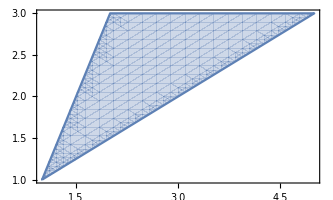
Solución:
Las rectas que pasan por los vértices son:
(2,3) y (5,3): y=3.
(1,1) y (2,3): y=2x-1, o lo que es lo mismo, x=(y+1)/2.
(1,1) y (5,3): y=(x+1)/2, o lo que es lo mismo, x= 2y-1.

-Graphics-
Observando la región, vemos que si consideramos la variación de la y, en el intervalo [1,3], podemos dejar la x variando en [(y+1)/2, 2y-1]. Así tenemos que calcular una sola integral doble: 
∫_1^3 (∫_((y+1)/2)^(2y-1) 2 x^2+3yⅆx)ⅆy=∫_1^3 (2x^3/3+3y x)|_(x=(y+1)/2)^(x=2y-1)ⅆy =  ∫_1^3 (2(2y-1)^3/3+3y (2y-1))-(2((y+1)/2)^3/3+3y (y+1)/2))ⅆy =   ∫_1^3 (3/4 (-1-y-5 y^2+7 y^3))ⅆy = 3/4 (-y-y^2/2-5 y^3/3+7 y^4/4)|_(y=1)^(y=3)=3/4 (-3-9/2-5*27/3+7*81/4)-3/4 (-1-1/2-5/3+7/4) = 3/4 (-2-8/2-130/3+7*80/4) = 3/4 (-6-130/3+140) =3/4 (134-130/3) =3/12*272 = 68

Con Mathematica:

```mathematica
∫_1^3 (∫_((y+1)/2)^(2y-1) (2 x^2+3y)ⅆx)ⅆy
```

68

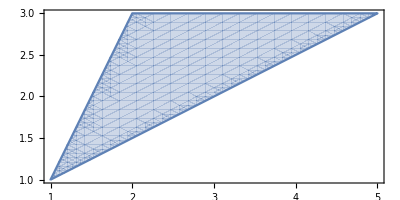

```mathematica
RegionPlot[1≤y≤3&&(y+1)/2≤x≤2y-1,{x,1,5},{y,1,3},AspectRatio->Automatic]
```

## 25.- (Enero 2022) Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=x^4+y^2-8 x^2-2.

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 4 x^3-16x =4x( x^2-4) = 0 ⟹ x=0, x= 2, x=-2
		∂_y f(x,y) = 2y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (0,0), (2,0), (-2,0).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(12 x^2-16 | 0
0 | 2)|
Hessiano (0,0) = |(-16 | 0
0 | 2)|= -32 < 0 (Punto de silla)
Hessiano (2,0) = |(32 | 0
0 | 2)|= 64 > 0 (máximo o mínimo relativo) (Como ∂_(x,x) f(2,0)= 32 >0, será mínimo local)
Hessiano (-2,0) = |(32 | 0
0 | 2)|= 64 > 0 (máximo o mínimo relativo) (como ∂_(x,x) f(-2,0)=32>0, será mínimo local)

Como el hessiano en el punto (0,0) es negativo, habrá un punto de silla. Como el hessiano en los puntos (2,0) y (-2,0) es positivo habrá un mínimo o un máximo relativo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en ese punto. Como la derivada segunda es 32 >0, hay un mínimo relativo en esos dos puntos.
Con Mathematica podemos dibujar la gráfica.

```mathematica
Plot3D[x^4+y^2-8x^2-2,{x,-3,3},{y,-1,1}]
```

-Graphics3D-

## 26.- (Enero 2022) Calcular los extremos absolutos (máximos y mínimos) de la función f(x,y)=x^3-2 y^2 en el conjunto de puntos que cumplen x^2+y^2≤1.

Solución:
La función es polinómica y, por tanto, es continua y derivable. Los extremos pueden estar en el interior del círculo (x^2+y^2<1), o en el borde (en la circunferencia x^2+y^2=1).
Para encontrar los posibles puntos en el interior, hacemos derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 3 x^2 =0 ⟹ x=0
		∂_y f(x,y) = -4y = 0 ⟹ y=0
Las derivadas parciales se anulan en el punto (0,0) que está en el interior del recinto (0^2+0^2<1).

Ahora hay que estudiar los posibles puntos en el borde del recinto; cuando x^2+y^2=1. Podemos buscar los posibles puntos siguiendo dos ideas:
1) Multiplicadores de Lagrange:
Consideramos F(x,y,t) = f(x,y) + t g(x,y)
donde f(x,y)=x^3-2 y^2, g(x,y)=x^2+y^2-1.

		∂_x F(x,y,t) = 3 x^2 + t(2x) = x( 3x + 2t) = 0 
		∂_y F(x,y,t) = -4y+t(2y) = 2y(t-2) = 0
		∂_t F(x,y,t) = x^2+y^2-1 = 0
 La segunda ecuación se cumple cuando y=0 ó t=2. Consideremos cada caso:
 a) Si y=0, de la tercera ecuación sacamos que x=1 ó x=-1. En el caso x=1, la primera ecuación se cumpliría si t=-3/2. Si x =-1, la primera ecuación se cumpliría si t= 3/2. Por tanto, obtendríamos las soluciones (x,y,t)= (1,0,-3/2), (-1,0,3/2).
 b) Si t=2, la primera ecuación quedaría como  3 x^2 + 4x= x(3x+4)=0. Se cumpliría cuando x=0 ó x=-4/3. Cuando x=0, la tercera ecuación se cumpliría si y=1 ó y=-1. Cuando x=-4/3, la tercera ecuación no se cumpliría. Por tanto, obtenemos las soluciones (0,1,2) y (0,-1,2).
 
Al punto interior del círculo (0,0) debemos añadir los cuatro encontrados en el borde, (1,0), (-1,0), (0,1), (0,-1). Evaluando la función f , obtenemos:
 f(0,0)=0^3-2*0^2=0, f(1,0)=1^3-2*0^2=1, f(-1,0)=(-1)^3-2*0^2=-1, f(0,1)=0^3-2*1^2=-2, f(0,-1)=0^3-2*(-1)^2=-2.
 
El máximo absoluto se encuentra en el punto (1,0) con un valor de 1, y el mínimo absoluto se alcanza en los puntos (0,1) y (0,-1) con un valor de -2.
 
Veamos ahora otra forma de estudiar el borde.
2) Se trata de buscar los posibles máximos y mínimos de f(x,y)=x^3-2 y^2 cuando x^2+y^2=1. Podríamos despejar y^2 y sustituir en la función. Tenemos que y^2=1-x^2, por tanto  f(x,y)=x^3-2(1-x^2)=x^3+2 x^2-2 que sería una función de una variable, x. Esta variable x puede moverse en el intervalo [-1,1] (para que pueda cumplirse que x^2+y^2=1).
Los extremos de x^3+2 x^2-2, en [-1,1] se encontrarían en los extremos del intervalo o en los puntos con derivada cero. La derivada es:
3 x^2+4x = x (3x+4) =0. La derivada se anula cuando x=0 ó x=-4/3. Este último valor no pertenece al intervalo. Por tanto, nos quedamos con los valores de los extremos, x=1 y x=-1 y el punto de derivada cero, x=0. Como debe cumplirse que x^2+y^2=1, los puntos candidatos a máximos o mínimos serían: (1,0) (-1,0), (0,1) y (0,-1).

Evaluamos la función f(x,y) en los cinco puntos posibles:  
 f(0,0)=0^3-2*0^2=0, f(1,0)=1^3-2*0^2=1, f(-1,0)=(-1)^3-2*0^2=-1, f(0,1)=0^3-2*1^2=-2, f(0,-1)=0^3-2*(-1)^2=-2.

El máximo absoluto se encuentra en el punto (1,0) con un valor de 1, y el mínimo absoluto se alcanza en los puntos (0,1) y (0,-1) con un valor de -2.
Con el Mathematica dibujamos la gráfica:

```mathematica
Plot3D[Which[x^2+y^2<=1,x^3-2y^2],{x,-1,1},{y,-1,1},PlotPoints->50]
```

-Graphics3D-

## 27.- (Enero 2022) Dada la función f(x,y) = 3x^3y^2 + 2x cos y + y, calcular la ecuación del plano tangente a la gráfica de la función en el punto (1,0) y utilizarlo para estimar el valor de f(0.5, 0.5).

Solución:
La ecuación del plano tangente a la gráfica de una función de dos variables es similar a la ecuación de la recta tangente a la gráfica de una función de una variable, añadiendo un nuevo sumando. En este caso, sería:

		z=f(1,0) + ∂_x f(1,0) (x-1)+∂_y f(1,0) (y-0)
Calculamos el valor de f en el punto y sus derivadas parciales:
f(x,y) = 3x^3y^2 + 2x cos y + y
f(1,0) = 3*1^3*0^2 + 2*1* cos 0 + 0 = 0+2+0 = 2
∂_x f(x,y)= 9x^2y^2 + 2 cos y
∂_x f(1,0)= 9*1^2*0^2 + 2 cos 0 = 2
∂_y f(x,y)= 6x^3y -2x sen y + 1
∂_y f(1,0)= 6*1^3*0 -2*1* sen 0 + 1 = 1

z=f(1,0) + ∂_x f(1,0) (x-1)+∂_y f(1,0) (y-0)= 2 + 2 (x-1)+1 (y-0)= 2 + 2x-2+y = 2x+y

El valor de f(0.5,0.5) se puede aproximar utilizando el polinomio anterior y obtenemos 2*0.5+0.5=1.5

Con el Mathematica:

```mathematica
f[x_,y_]:= 3 x^3 y^2+ 2 x Cos[y]+y
```

```mathematica
f[1,0]+(D[f[x,y],x]/.{x->1,y->0}) (x-1)+(D[f[x,y],y]/.{x->1,y->0}) (y-0)//Simplify
```

2 x+y

```mathematica
Plot3D[{f[x,y],2x+y},{x,0,1.5},{y,-1,1}]
```

-Graphics3D-

```mathematica
{f[x,y],2x+y}/.{x->0.5,y->0.5}
```

{1.47133,1.5}

## 28.- (Julio 2022) Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=x^3+2 y^2-3x+4.

Solución:
La función f(x,y)=x^3+2 y^2-3x+4 es una función polinómica, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 3 x^2-3 = 3( x^2-1) = 0 ⟹ x=1, x= -1
		∂_y f(x,y) = 4y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (1,0) y (-1,0).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(6x | 0
0 | 4)|
Hessiano (1,0) = |(6 | 0
0 | 4)|= 24 > 0 (máximo o mínimo relativo) (Como ∂_(x,x) f(1,0)= 6 >0, será mínimo local)
Hessiano (-1,0) = |(-6 | 0
0 | 4)|= -24 < 0 (Punto de silla)

Como el hessiano en el punto (-1,0) es negativo, habrá un punto de silla. Como el hessiano en el punto (1,0) es positivo habrá un mínimo o un máximo relativo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en ese punto. Como la derivada segunda es 6 >0, hay un mínimo relativo en ese punto.

## 29.- (Enero 2018) Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=(x^2-4)^2+ y^2.

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2(x^2-4)2x = 0 ⟹ x=0 ó x^2-4= 0 ⟹ x=0, 2, -2
		∂_y f(x,y) = 2y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (0,0), (2,0) y (-2,0).
Para ver si son máximos, mínimos y puntos de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(12 x^2-16 | 0
0 | 2)|
Hessiano (0,0) = |(-16 | 0
0 | 2)|= -32 < 0

Hessiano (2,0) = |(32 | 0
0 | 2)|= 64 > 0
Hessiano (-2,0) = |(32 | 0
0 | 2)|= 64 > 0

Como el hessiano en el punto (0,0) es negativo, en el punto (0,0) hay un punto de silla.

Como el hessiano en los puntos (2,0) y (-2,0) es positivo habrá un máximo o un mínimo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en esos puntos. Como la derivada segunda es 32 >0, hay mínimos relativos en esos puntos.

## 30.- (Junio 2021) Calcular los extremos relativos de la función f(x,y)= -x^2+2x+y^2-2y+2x y + 4.

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = -2x+2+2y = 0  ⟹ x-y=1 
		∂_y f(x,y) = 2y-2+2x = 0 ⟹ x+y=1
Resolvemos el sistema, en este caso se trata de dos ecuaciones lineales. Podemos sumar las dos ecuaciones y obtenemos x=1. Después obtenemos y=0.
 
El punto donde se anulan las dos derivadas parciales es (1,0).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(-2 | 2
2 | 2)|
Hessiano (1,0) = |(-2 | 2
2 | 2)|= -8 < 0

Como el hessiano en el punto (1,0) es negativo, en ese punto hay un punto de silla.

## 31.- (Enero 2019) Calcular los máximos y mínimos absolutos de la función f(x,y)=x^2-y^2 en el recinto dado por x^2+ 2 y^2≤ 1.

Solución:
Los máximos o mínimos pueden estar en el interior de la elipse (cuando x^2+ 2 y^2< 1) o en el borde (x^2+ 2 y^2= 1).
Para el interior, hacemos derivadas parciales y calculamos dónde se anulan:
∂_x f= 2x=0, ∂_y f= -2y=0 ⟹ x=0, y=0. Las derivadas parciales se anulan en el punto (0,0) que está dentro de la elipse pues  0^2+ 2*0^2< 1.
Respecto al borde utilizamos la técnica de los multiplicadores de Lagrange. Para ello consideramos F(x,y,λ)=x^2-y^2 + λ(x^2+ 2 y^2- 1). Haciendo derivadas parciales e igualando a cero tenemos:
∂_x F= 2x +2xλ=0 ⟹x(1+λ)=0 
∂_y F= -2y + 4yλ=0  ⟹y(-1+2λ)=0  
∂_λ F= x^2+ 2 y^2- 1=0
De la primera ecuación, una posibilidad es x=0. En este caso, de la tercera ecuación, y=±√(1/2). Con lo cual, para que se cumpla también la segunda ecuación λ debe ser 1/2. Obtenemos así unos puntos posibles (0,√(1/2)),  (0,-√(1/2)).
De la primera ecuación, si x no es cero, tenemos que λ=-1, entonces la segunda ecuación quedaría como -3y=0. Por tanto, y=0. Ahora en la tercera ecuación, x=±1. Por tanto aparecen los puntos (1,0) y (-1,0).
Juntando los cinco puntos candidatos, evaluamos la función f en ellos y obtenemos:
f(0,0)=0, f(1,0)=1, f(-1,0)=1, f(0,√(1/2))=-1/2,  f(0,-√(1/2))=-1/2.
De donde concluimos que f, en el recinto dado, tiene máximos absolutos en (1,0) y (-1,0) y mínimos absolutos en (0,√(1/2)) y  (0,-√(1/2)).

## 32.- (Enero 2019) Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=(x^2(x-2))^2+ y^2.

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2(x(x-2))^2 + 2x^2(x-2)= 2x(x-2)(x-2+x) =0 ⟹ x=0, (x-2)=0 ó (x-2+x)=0 ⟹ x=0, 2, 1
		∂_y f(x,y) = 2y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (0,0), (2,0) y (1,0).
Para ver si son máximos, mínimos y puntos de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(12 x^2-24x+8 | 0
0 | 2)|
Hessiano (0,0) = |(8 | 0
0 | 2)|= 16 > 0

Hessiano (2,0) = |(8 | 0
0 | 2)|= 16 > 0
Hessiano (1,0) = |(-4 | 0
0 | 2)|= -8 < 0

Como el hessiano en los puntos (0,0) y (2,0) es positivo habrá un máximo o un mínimo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en esos puntos. Como la derivada segunda es 8 >0, hay mínimos relativos en esos puntos.

Como el hessiano en el punto (1,0) es negativo, en el punto (1,0) hay un punto de silla.

## 33.- (Enero 2021) Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=x^2+2x+y^2-4y+8.

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2x+2 = 0 ⟹ x= -1
		∂_y f(x,y) = 2y-4 = 0 ⟹ y=2
El punto donde se anulan las dos derivadas parciales es (-1,2).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(2 | 0
0 | 2)|
Hessiano (-1,2) = |(2 | 0
0 | 2)|= 4 > 0

Como el hessiano en el punto (-1,2) es positivo, en ese punto hay un mínimo o un máximo relativo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en ese punto. Como la derivada segunda es 2 >0, hay un mínimo relativo en ese punto.

## 34.- (Enero 2020) Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)= x^4 + y^4 - 4xy +1.

Solución:
Calculamos las derivadas parciales e igualamos a 0,
∂_x f[x,y] = 4 x^3-4 y = 0
∂_y f[x,y] = -4 x+4 y^3 = 0
Resolvemos el sistema, y=x^3, x=y^3, por tanto, x=y^3=x^9, de donde x(1-x^8)=0, x=0, 1, -1. Los puntos donde se anulan las derivadas parciales son (0,0), (1,1), (-1,-1).
Haciendo las derivadas segundas,
∂_(x,x) f[x,y] = 12 x^2
∂_(x,y) f[x,y] = -4
∂_(y,x) f[x,y] = -4
∂_(y,y) f[x,y] = 12 y^2 
Hess(x,y)=(12 x^2 | -4
-4 | 12 y^2) 
En el punto (0,0) el determinante es negativo, por tanto hay un punto de silla. En los puntos (1,1) y (-1,-1), el determinante es positivo y la derivada segunda respecto a x, es positiva, luego son mínimos relativos.

## 35.- (Enero 2021) Calcular la integral de la función f(x,y)= x^2+y en el rectángulo de vértices (0,0), (2,0), (0,1) y (2,1).

Solución:
∫_0^2 (∫_0^1 x^2+yⅆy)ⅆx= ∫_0^2 (x^2 y+y^2/2)|_(y=0)^(y=1)ⅆx =  ∫_0^2 (x^2*1+1^2/2- (x^2*0+0^2/2))ⅆx =  ∫_0^2 (x^2+1/2)ⅆx = (x^3/3+x/2)|_(x=0)^(x=2) = (2^3/3+2/2)- (0^3/3+0/2)= (8/3+1)=11/3

Con Mathematica

```mathematica
Integrate[Integrate[x^2+y,{x,0,2}],{y,0,1}]
```

11/3

## 36.- (Junio 2021) Calcular la integral de la función f(x,y)= x^2+y en el triángulo de vértices (-1,0), (0,2) y (1,0).

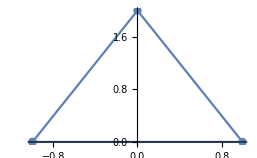
Solución:
Observamos el triángulo determinado por los puntos que nos da el problema.
-Graphics-
Las rectas que delimitan el triángulo son y=0, y=2x+2, y=2-2x.
Podríamos calcular la integral de dos formas. 
1) Observamos que la variable x varía entre -1 y 1. Para cada valor de x entre -1 y 0, la variable y varía entre 0 y 2x+2. En cambio, para cada valor de x entre 0 y 1, la variable y se mueve entre 0 y 2-2x.
2) Por otra parte, si pensamos que la variable y se mueve entre 0 y 2, podemos ver que la variable x está entre (y-2)/2 y (2-y)/2.

Así, siguiendo la primera vía la integral sería:

 ∫_-1^0 (∫_0^(2x+2) x^2+yⅆy)ⅆx + ∫_0^1 (∫_0^(-2x+2) x^2+yⅆy)ⅆx.
 
 Realizamos los cálculos:

 ∫_-1^0 (∫_0^(2x+2) x^2+yⅆy)ⅆx= ∫_-1^0 (x^2 y+y^2/2)|_(y=0)^(y=2x+2)ⅆx =  ∫_-1^0 (x^2*(2x+2)+(2x+2)^2/2- (x^2*0+0^2/2))ⅆx =  ∫_-1^0 (2 x^3+ 2 x^2+2 x^2+4x+2)ⅆx =   ∫_-1^0 (2 x^3+ 4 x^2+4x+2)ⅆx = x^4/2+ 4 x^3/3+2 x^2+2x|_(x=-1)^(x=0) = (0^4/2+ 4 0^3/3+2*0^2+2*0) - ((-1)^4/2+ 4(-1)^3/3+2(-1)^2+2(-1)) = -1/2+4/3-2+2 = (-3+8)/6= 5/6.

∫_0^1 (∫_0^(-2x+2) x^2+yⅆy)ⅆx= ∫_0^1 (x^2 y+y^2/2)|_(y=0)^(y=-2x+2)ⅆx =  ∫_0^1 (x^2*(-2x+2)+(-2x+2)^2/2- (x^2*0+0^2/2))ⅆx =  ∫_0^1 (-2 x^3+ 2 x^2+2 x^2-4x+2)ⅆx =   ∫_0^1 (-2 x^3+ 4 x^2-4x+2)ⅆx = -x^4/2+ 4 x^3/3-2 x^2+2x|_(x=0)^(x=1) = (-1^4/2+ 4 1^3/3-2*1^2+2*1) - (-0^4/2+ 4 0^3/3.2*0^2+2*0) = -1/2+4/3-2+2 = (-3+8)/6= 5/6.

El resultado sería  5/6 +  5/6 =  10/6 =  5/3

Siguiendo la segunda vía tendríamos:

∫_0^2 (∫_((y-2)/2)^((2-y)/2) x^2+yⅆx)ⅆy= ∫_0^2 (x^3/3+y x)|_(x=(y-2)/2)^(x=(2-y)/2)ⅆy =  ∫_0^2 (((2-y)/2)^3/3+y (2-y)/2- (((y-2)/2)^3/3+y (y-2)/2 ))ⅆy =  ∫_0^2 ((2-y)^3/24+(2y-y^2)/2 -(y-2)^3/24-(y^2-2y)/2 )ⅆy =  ∫_0^2 (2-y)^3/12+(2y-y^2) ⅆy= -(2-y)^4/48+y^2-y^3/3|_(y=0)^(y=2) = -(2-2)^4/48+2^2-2^3/3+(2-0)^4/48-0^2+0^3/3 =  4-8/3+16/48 =4-8/3+1/3=4-7/3 = 5/3

Con Mathematica

```mathematica
Integrate[Integrate[x^2+y,{x,(y-2)/2,(2-y)/2}],{y,0,2}]
```

5/3

## 37.- (Junio 2018) Calcular el valor de la integral de la función f(x,y) = x+2y en el paralelogramo de vértices (1,1), (2,1), (2,2), (3,2).

Solución:
Pintemos el recinto con Mathematica

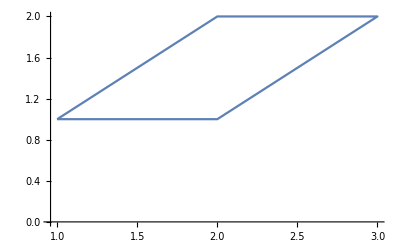

```mathematica
ListPlot[{{1,1},{2,1},{3,2},{2,2},{1,1}}, Joined->True]
```

Tenemos dos posibilidades:
OPCIÓN 1. Cuando la x se mueve en el intervalo [1,2] la y se mueve entre las rectas y=1 e y=x, pero cuando la x se mueve en el intervalo [2,3] la y se mueve entre las rectas y=x-1 e y=2. De esta forma: 
∫_1^2 (∫_1^x (x+2y)ⅆy)ⅆx+∫_2^3 (∫_(x-1)^2 (x+2y)ⅆy)ⅆx=∫_1^2 [xy+y^2]_1^x ⅆx+∫_2^3 [xy+y^2]_(x-1)^2 ⅆx=∫_1^2 (x^2+x^2-x-1)ⅆx+∫_2^3 (2x+4-x(x-1)-(x-1)^2)ⅆx=∫_1^2 (2 x^2-x-1)ⅆx+∫_2^3 (-2 x^2+5x+3)ⅆx=[(2 x^3)/3-x^2/2-x]_1^2+[(-2 x^3)/3+(5 x^2)/2+3x]_2^3=(16/3-2-2-2/3+1/2+1)+(-18+45/2+9+16/3-10-6)=13/6+17/6=5 

OPCIÓN 2. Cuando la y se mueve en el intervalo [1,2] la x se mueve entre las rectas x=y y x=y+1. Así
∫_1^2 (∫_y^(y+1) (x+2y)ⅆx)ⅆy=∫_1^2 [x^2/2+2xy]_y^(y+1)ⅆy=∫_1^2 ((y+1)^2/2+2(y+1)y-y^2/2-2yy)ⅆy=∫_1^2 (3y+1/2)ⅆy=[(3 y^2)/2+y/2]_1^2=(3*2^2)/2+1-(3*1^2)/2-1/2=5

Con Mathematica

```mathematica
Integrate[Integrate[x+2y,{y,1,x}],{x,1,2}]+Integrate[Integrate[x+2y,{y,x-1,2}],{x,2,3}]
```

5

```mathematica
Integrate[Integrate[x+2y,{x,y,y+1}],{y,1,2}]
```

5

## 38.- (Enero 2018. Prácticas) Calcular la integral de la función f(x,y)= 1-x-y en el triángulo de vértices (0,0), (1,0) y (0,1), para obtener el volumen de la siguiente figura. -Graphics3D-

Solución:
Pintemos el recinto con Mathematica

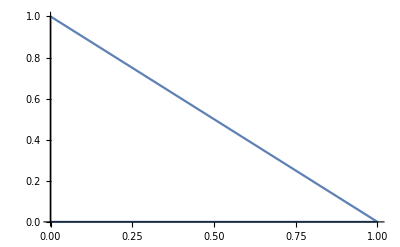

```mathematica
ListPlot[{{0,0},{1,0},{0,1},{0,0}}, Joined->True]
```

Tenemos dos posibilidades:
OPCIÓN 1. Cuando la x se mueve en el intervalo [0,1] la y se mueve entre las rectas y=0 y la recta que une los puntos (1,0) y (0,1).
Aplicando la definición de recta punto pendiente, sabemos que la pendiente de la recta viene dada por m=(1-0)/(0-1)=-1 y por tanto la ecuación de la recta es y=-1(x-1)=1-x

∫_0^1 (∫_0^(1-x) (1-x-y)ⅆx)ⅆy=∫_0^1 [y-xy-y^2/2]_0^(1-x)ⅆx=∫_0^1 ((1-x)-x(1-x)-(1-x)^2/2)ⅆx=∫_0^1 (x^2/2-x+1/2)ⅆx=[x^3/6-x^2/2+x/2]_0^1=(1/6-1/2+1/2)=1/6 

OPCIÓN 2. Cuando la y se mueve en el intervalo [0,1] la x se mueve entre las rectas x=0 y la recta que une los puntos (1,0) y (0,1).
Aplicando la definición de recta punto pendiente, sabemos que la pendiente de la recta viene dada por m=(1-0)/(0-1)=-1 y por tanto la ecuación de la recta es y=-1(x-1)=1-x, luego x=1-y
∫_0^1 (∫_0^(1-y) (1-x-y)ⅆx)ⅆy=∫_0^1 [x-x^2/2-xy]_0^(1-y)ⅆy=∫_0^1 ((1-y)-(1-y)^2/2-y(1-y))ⅆy=∫_0^1 (y^2/2-y+1/2)ⅆy=[y^3/6-y^2/2+y/2]_0^1=(1/6-1/2+1/2)=1/6

Con Mathematica

```mathematica
∫_0^1 (∫_0^(1-x) (1-x-y)ⅆy)ⅆx
```

1/6

```mathematica
∫_0^1 (∫_0^(1-y) (1-x-y)ⅆx)ⅆy
```

1/6

## 39.- (Enero 2018. Prácticas) Calcular la integral de la función f(x,y)= x^2+y^2 en el triángulo de vértices (0,0), (1,0) y (0,1), para obtener el volumen de la siguiente figura. -Graphics3D-

Solución: 
El conjunto donde tenemos que realizar la integral es el triángulo de vértices (0,0), (1,0) y (1,1).

```mathematica
ListPlot[{{0,0},{1,0},{0,1},{0,0}}, Joined->True]
```

-Graphics-

En este caso, podemos considerar una cualquiera de las variables, por ejemplo la x. La variable x se mueve entre 0 y 1. Una vez fijado el valor de x, entre 0 y 1. El valor de y se moverá entre 0 y x. La variable y se movería desde el 0 hasta el punto de la recta que une (0,0) y (1,1). Se trata de la recta y=x.

∫_0^1 (∫_0^x (x^2+y^2)ⅆy)ⅆx=∫_0^1 [x^2 y+y^3/3]_0^x ⅆx=∫_0^1 (4 x^3)/3 ⅆx=[x^4/3]_0^1=1/3

Con Mathematica

```mathematica
∫_0^1 ∫_0^x (x^2+y^2)ⅆyⅆx
```

1/3

## 40.- Calcular ∫∫_D (x^2-y^2)ⅆyⅆx siendo D el recinto comprendido entre las gráficas de y = (a+1) x e y = x^2, siendo a el último dígito numérico de su DNI.

Solución:
Tomamos, por ejemplo, a=4. Así el recinto esta comprendido entre las curvas y=5x e y=x^2. Buscamos los puntos donde se cortan ambas curvas

5x=x^2⟹x^2-5x=0⟹x(x-5)=0⟹{x=0⟹y=0
x=5⟹y=25 Las curvas se cortan en los puntos (0,0) y (5,25)

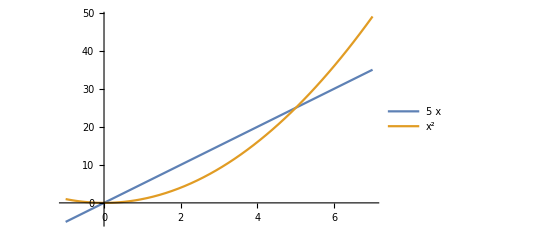

```mathematica
Plot[{5x,x^2},{x,-1,7},PlotLegends->"Expressions"]
```

Por tanto, mientras la x se mueve en el intervalo [0,5] la y se mueve entre las curvas y=5x e y=x^2. Así

∫_0^5 (∫_(5x)^(x^2) (x^2+y^2)ⅆy)ⅆx=∫_0^5 [x^2 y+y^3/3]_(5x)^(x^2)ⅆx=∫_0^5 (x^4+x^6/3-5 x^3-(125 x^3)/3)ⅆx=∫_0^5 (x^6/3+x^4-(140 x^3)/3)ⅆx=[x^7/21+x^5/5-(35 x^4)/3]_0^5=-20625/7

Con Mathematica

```mathematica
Integrate[Integrate[x^2+y^2,{y,5x,x^2}],{x,0,5}]
```

-20625/7

## 41.- La integral de la función f(x,y)= x^2+2 y^2 en el triángulo de vértices (0,0), (1,0) y (0,1) es.

Solución:
Pintemos el recinto con Mathematica

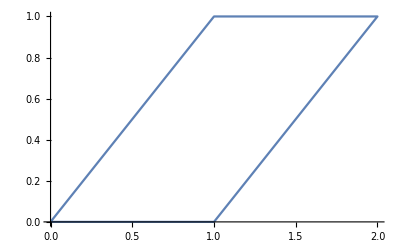

```mathematica
ListPlot[{{0,0},{1,0},{2,1},{1,1},{0,0}}, Joined->True]
```

El recinto se trata de un rombo. Para obtener el valor de la integral tenemos dos posibilidades:

OPCIÓN 1. Cuando la x se mueve en el intervalo [0,1] la y se mueve entre las recta y=0 y la recta que une los puntos (0,0) y (1,1), es decir la recta y=x, pero cuando la x se mueve en el intervalo [1,2] la y se mueve entre la recta que une los puntos (1,0) y (2,1), es decir la recta y=x-1 y la recta y=1. De esta forma: 
∫_0^1 (∫_0^x ( x^2+2 y^2)ⅆy)ⅆx+∫_1^2 (∫_(x-1)^1 ( x^2+2 y^2)ⅆy)ⅆx=∫_0^1 [x^2 y+(2 y^3)/3]_0^x ⅆx+∫_1^2 [x^2 y+(2 y^3)/3]_(x-1)^2 ⅆx=∫_0^1 (x^3+(2 x^3)/3)ⅆx+∫_1^2 (2 x^2+16/3-x^2(x-1)-(2(x-1)^3)/3)ⅆx=∫_0^1 (5 x^3)/3 ⅆx+∫_1^2 ((-5 x^3)/3+4 x^2-2x+4/3)ⅆx=[(5 x^4)/12]_0^1+[(-5 x^4)/3+(4 x^3)/3-x^2+(4x)/3]_1^2=5/12+17/12=11/6 

OPCIÓN 2. Cuando la y se mueve en el intervalo [0,1] la x se mueve entre las rectas x=y y x=y+1. Así
∫_0^1 (∫_y^(y+1) ( x^2+2 y^2)ⅆx)ⅆy=∫_0^1 [x^3/3+2 xy^2]_y^(y+1)ⅆy=∫_0^1 ((y+1)^3/3+2(y+1)y^2-y^3/3-2 yy^2)ⅆy=∫_0^1 (3 y^2+y+1/3)ⅆy=[y^3+y^2/2+y/3]_0^1=1+1/2+1/3=11/6

Con Mathematica

```mathematica
Integrate[Integrate[x^2+2y^2,{y,0,x}],{x,0,1}]+Integrate[Integrate[x^2+2y^2,{y,x-1,1}],{x,1,2}]
```

11/6

```mathematica
Integrate[Integrate[x^2+y^2,{x,y,y+1}],{y,0,1}]
```

3/2

## 42.- (Enero 2019. Prácticas) Calcular la integral de la función f(x,y)= x^2+y^2 en el cuadrilátero de vértices (0,0), (1,0), (2,1) y (1,1)

Solución:
Pintemos el recinto con Mathematica

```mathematica
ListPlot[{{0,0},{1,0},{2,1},{1,1},{0,0}}, Joined->True]
```

-Graphics-

El recinto se trata de un rombo. Para obtener el valor de la integral tenemos dos posibilidades:

OPCIÓN 1. Cuando la x se mueve en el intervalo [0,1] la y se mueve entre las recta y=0 y la recta que une los puntos (0,0) y (1,1), es decir la recta y=x, pero cuando la x se mueve en el intervalo [1,2] la y se mueve entre la recta que une los puntos (1,0) y (2,1), es decir la recta y=x-1 y la recta y=1. De esta forma: 
∫_0^1 (∫_0^x ( x^2+y^2)ⅆy)ⅆx+∫_1^2 (∫_(x-1)^1 ( x^2+y^2)ⅆy)ⅆx=∫_0^1 [x^2 y+y^3/3]_0^x ⅆx+∫_1^2 [x^2 y+y^3/3]_(x-1)^2 ⅆx=∫_0^1 (x^3+x^3/3)ⅆx+∫_1^2 (2 x^2+8/3-x^2(x-1)-(x-1)^3/3)ⅆx=∫_0^1 (4 x^3)/3 ⅆx+∫_1^2 ((-4 x^3)/3+3 x^2-x+2/3)ⅆx=[x^4/3]_0^1+[-x^4/3+x^3-x^2/2+(2x)/3]_1^2=(1/3)+(-16/3+8-2+4/3+1/3-1+1/2-2/3)=3/2 

OPCIÓN 2. Cuando la y se mueve en el intervalo [0,1] la x se mueve entre las rectas x=y y x=y+1. Así
∫_0^1 (∫_y^(y+1) ( x^2+y^2)ⅆx)ⅆy=∫_0^1 [x^3/3+xy^2]_y^(y+1)ⅆy=∫_0^1 ((y+1)^3/3+(y+1)y^2-y^3/3-yy^2)ⅆy=∫_0^1 (2 y^2+y+1/3)ⅆy=[(2 y^3)/3+y^2/2+y/3]_0^1=2/3+1/2+1/3=3/2

Con Mathematica

```mathematica
Integrate[Integrate[x^2+y^2,{y,0,x}],{x,0,1}]+Integrate[Integrate[x^2+y^2,{y,x-1,1}],{x,1,2}]
```

3/2

```mathematica
Integrate[Integrate[x^2+y^2,{x,y,y+1}],{y,0,1}]
```

3/2

## 43.- Calcular la integral de la función f(x,y)= 2 x^2+y^2 en el cuadrilátero de vértices (0,0), (1,0), (2,1) y (1,1)

Solución:
Pintemos el recinto con Mathematica

```mathematica
ListPlot[{{0,0},{1,0},{2,1},{1,1},{0,0}}, Joined->True]
```

-Graphics-

El recinto se trata de un rombo. Para obtener el valor de la integral tenemos dos posibilidades:

OPCIÓN 1. Cuando la x se mueve en el intervalo [0,1] la y se mueve entre las recta y=0 y la recta que une los puntos (0,0) y (1,1), es decir la recta y=x, pero cuando la x se mueve en el intervalo [1,2] la y se mueve entre la recta que une los puntos (1,0) y (2,1), es decir la recta y=x-1 y la recta y=1. De esta forma: 
∫_0^1 (∫_0^x (2 x^2+y^2)ⅆy)ⅆx+∫_1^2 (∫_(x-1)^1 (2 x^2+y^2)ⅆy)ⅆx=∫_0^1 [2 x^2 y+y^3/3]_0^x ⅆx+∫_1^2 [2 x^2 y+y^3/3]_(x-1)^2 ⅆx=∫_0^1 (2 x^3+x^3/3)ⅆx+∫_1^2 (4 x^2+16/3-2x^2(x-1)-(x-1)^3/3)ⅆx=∫_0^1 (7 x^3)/3 ⅆx+∫_1^2 ((-7 x^3)/3+5 x^2-x+2/3)ⅆx=[(7 x^4)/12]_0^1+[(-7 x^4)/12+(5 x^3)/3-x^2/2+(2x)/3]_1^2=7/12+25/12=8/3 

OPCIÓN 2. Cuando la y se mueve en el intervalo [0,1] la x se mueve entre las rectas x=y y x=y+1. Así
∫_0^1 (∫_y^(y+1) ( 2 x^2+y^2)ⅆx)ⅆy=∫_0^1 [(2 x^3)/3+xy^2]_y^(y+1)ⅆy=∫_0^1 ((2(y+1)^3)/3+(y+1)y^2-(2 y^3)/3-yy^2)ⅆy=∫_0^1 (3 y^2+2y+2/3)ⅆy=[y^3+y^2+(2y)/3]_0^1=1+1+2/3=8/3

Con Mathematica

```mathematica
Integrate[Integrate[2x^2+y^2,{y,0,x}],{x,0,1}]+Integrate[Integrate[2x^2+y^2,{y,x-1,1}],{x,1,2}]
```

8/3

```mathematica
Integrate[Integrate[2x^2+y^2,{x,y,y+1}],{y,0,1}]
```

8/3

## 44.- Calcular los máximos y mínimos absolutos de la función f(x,y)=2 x^2- y^2 en el recinto dado por x^2+ y^2≤ 1.

Solución:
La función es polinómica y, por tanto, es continua y derivable. Los extremos pueden estar en el interior del circulo (x^2+y^2⩽1), o en el borde (en la circunferencia x^2+y^2=1).

Para encontrar los posibles puntos en el interior, hacemos derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 4x =0 ⟹ x=0
		∂_y f(x,y) = -2y = 0 ⟹ y=0
En este caso se obtienen un único punto candidato a extremo el punto (0,0), que si pertenece al recinto ya que 0^2+0^2=0<1

Ahora hay que estudiar los posibles puntos en el borde del recinto; cuando x^2+y^2=1. Buscamos los posibles puntos siguiendo los multiplicadores de Lagrange:
Consideramos F(x,y,t) = f(x,y) + t g(x,y)
donde f(x,y)=2 x^2- y^2, g(x,y)=x^2+y^2-1, luego F(x,y,t)=2 x^2- y^2+t*(x^2+y^2-1)

		∂_x F(x,y,t) = 4x + t*(2x)=2x(2+t)⟹2x(2+t)=0⟹{x=0
2+t=0⟹t=-2  
		∂_y F(x,y,t) =-2+ t*(2y)⟹-2+ 2yt=0⟹yt=1⟹y=1/t
		∂_t F(x,y,t) = x^2+y^2-1⟹x^2+y^2-1=0⟹{Si x=0⟹y^2-1=0⟹y=±1
Si t=-2⟹y=-1/2⟹x^2+1/4-1=0⟹x=±(√3)/2
		
En el borde hemos encontrado cuatro candidatos más los puntos: (0,-1), (0,1), ((√3)/2,-1/2) y (-(√3)/2,-1/2)

Evaluando la función f en los cinco puntos candidatos y obtenemos:
 f(0,0)=2*0^2- 0^2=0 
 f(0,-1)=2*0^2- (-1)^2=-1 
  f(0,1)=2*0^2- 1^2=-1
   f((√3)/2,-1/2)=2*((√3)/2)^2- (-1/2)^2=5/4
   f((√3)/2,-1/2)=2*(-(√3)/2)^2- (-1/2)^2=5/4
 
El máximo absoluto se encuentra en los puntos ((√3)/2,-1/2)y (-(√3)/2,-1/2)con un valor de 5/4, y el mínimo absoluto se alcanza en los puntos (0,-1) y (0,1) con un valor de -1.